```mathematica
n=3;
k=2;
```

### prune

```mathematica
getinfo[r_]:={
Transpose@{r[[All,1,2]],r[[All,2]]},
Graph[
r[[All,All,1]],
VertexLabels->Automatic
]
}
```

```mathematica
getinfo[rules[[1]]][[1,All,2]]
```

Part::partd: Part specification rules⟦1⟧ is longer than depth of object.

Part::partd: Part specification rules⟦1⟧⟦All,1,2⟧ is longer than depth of object.

Part::partd: Part specification rules⟦1⟧⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::pkspec1: The expression Integer[] cannot be used as a part specification.

{All,All}

```mathematica
transform[reachable_List,info_List]:=
Table[
Join@@
Table[
If[
MemberQ[reachable[[i]],j],
Flatten@info[[i,6*j-5;;6*j]],
ConstantArray[1,6]
],
{j,n}
],(* end Table over j *)
{i,Length[info]}
]
```

```mathematica
ctransform=Compile[
{{reachable,_Integer,2},{info,_Integer,2}},
Table[
Flatten@
Table[
If[
MemberQ[reachable[[i]],j],
Flatten@info[[i,6*j-5;;6*j]],
ConstantArray[1,6]
],
{j,n}
],(* end Table over j *)
{i,Length[info]}
],
CompilationTarget->"C",
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
```

```mathematica
prune[map_DataStructure,rules_List]:=
Module[
{info=getinfo/@rules,reachables,transL,reachable},
Print["getinfo done"];
reachables=AbsoluteTiming[PadLeft[VertexOutComponent[#,{1}],3,-1]&/@info[[All,2]]];
transL=AbsoluteTiming[
ctransform[reachables[[2]],
DeleteDuplicates[Length/@Partition[Flatten[info[[All,1,All,2]]],3*n*k]]//Print;
Partition[Flatten[info[[All,1,All,2]]],3*n*k]]
(*Table[
reachable=reachables[[2,i]];
Join@@
Table[
If[
MemberQ[reachable,j],
info[[i,1,8*j-7;;8*j]],
ConstantArray[0,8]
],
{j,n}
],(* end Table over j *)
{i,Length[info]}
](* end Table over i *)*)
];
map["Insert",(#->map["Lookup",#,0&]+1)]&/@transL[[2]];(*sequential*)
{reachables[[1]],transL[[1]]}
]
map=CreateDataStructure["HashTable"];
rules[[163;;164]];
AbsoluteTiming@prune[map,%]
```

Part::take: Cannot take positions 163 through 164 in $Aborted⟦2⟧.

{4.×10^-6,prune[DataStructure[…],$Aborted⟦2⟧⟦163;;164⟧]}

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

```mathematica
parallelprune[map_DataStructure,rules_List]:=
Module[
{info=Map[getinfo,rules],reachables,transL},
reachables=AbsoluteTiming[
ParallelMap[VertexOutComponent[#,{1}]&,info[[All,2]]]
];
transL=AbsoluteTiming[
ParallelTable[
Join@@(Take[info[[i,1]],{8*(#-1)+1,8*#}]&/@reachables[[2,i]]),
{i,Length[info]}
]
];
map["Insert",(#->map["Lookup",#,0&]+1)]&/@transL[[2]];(*sequential*)
{reachables[[1]],transL[[1]]}
]
```

```mathematica
lookup[map_DataStructure,rules_List]:=
Module[
{info=Map[getinfo,rules],reachables,transL},
reachables=VertexOutComponent[#,{1}]&/@info[[All,2]];transL=Table[
Join@@(Take[info[[i,1]],{8*(#-1)+1,8*#}]&/@reachables[[2]]),
{i,Length[info]}
];
map["Lookup",#]&/@transL
]
```

```mathematica
(2*n*k)^(n*k)
AbsoluteTiming[ParallelMap[tmRuleFromNum[#,n,k]&,Range[0,%-1]]];
rules=%[[2]];
%%[[1]]
Length[rules]
```

2985984

$Aborted

Part::partd: Part specification $Aborted⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

$Aborted⟦1⟧

2

```mathematica
Export["./wsrp/project/main/rules.mx",rules,"MX"]
```

./wsrp/project/main/rules.mx

```mathematica
map=CreateDataStructure["HashTable"];
AbsoluteTiming@prune[map,rules]
```

{6.×10^-6,prune[DataStructure[…],$Aborted⟦2⟧]}

```mathematica
elems=map["Elements"];
Length[%]
```

0

```mathematica
Export["./wsrp/project/main/elems.mx",elems,"MX"]
```

./wsrp/project/main/elems.mx

```mathematica
elems=Import["./wsrp/project/main/mx/elems.mx"];
```

```mathematica
elems[[1;;10]]
```

{{2,1,-1,2,0,1,3,1,-1,3,1,-1,3,0,1,2,1,1}→1,{2,1,1,2,0,1,3,1,1,2,0,1,2,0,1,3,0,-1}→1,{2,0,1,2,0,-1,3,1,-1,1,0,1,2,1,-1,2,0,-1}→1,{3,1,-1,2,0,1,1,0,-1,2,1,1,1,1,1,2,0,1}→1,{2,1,-1,3,1,-1,2,1,1,1,1,1,3,0,1,1,0,1}→1,{2,0,-1,3,0,1,1,0,-1,2,0,-1,1,1,1,2,0,-1}→1,{3,0,-1,2,0,-1,1,0,1,1,1,-1,1,1,-1,3,1,1}→1,{3,0,1,2,1,-1,1,1,-1,2,1,-1,2,0,1,1,0,1}→1,{2,1,-1,1,0,1,1,1,-1,3,1,1,3,1,1,3,0,-1}→1,{2,0,-1,3,1,1,1,1,1,3,1,-1,1,1,1,1,0,-1}→1}

We can confirm that equivalence classes come in sizes of  for all nonnegative : for , we indeed have , , .

```mathematica
Select[elems,!MatchQ[#[[2]],1|144|20736]&]
```

{}

## simulate

```mathematica
n=3;
k=2;
maxiters=64;
bits=4;
width=11;
```

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

### DO NOT DELETE: start archive v

```mathematica
hist[rule_Integer, num_Integer]:=
With[{min=Min[#[[All,1,2]],#[[1,1,2]]-width]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
(*1-width<=*)#[[1,3]]<=0,(* valid position *)
True,
MatchQ[#[[1,3]],1(*|-width*)],(* halt position *)
halt=True
]&
]
]&@TuringMachine[{rule,2,2},init[num],maxiters]
```

```mathematica
hist[302,14]
```

{{{1,12,0},{0,0,0,0,0,0,0,0,1,1,1,0}},{{2,11,-1},{0,0,0,0,0,0,0,0,1,1,1,0}},{{2,12,0},{0,0,0,0,0,0,0,0,1,1,0,0}},{{2,11,-1},{0,0,0,0,0,0,0,0,1,1,0,1}},{{2,10,-2},{0,0,0,0,0,0,0,0,1,1,1,1}},{{2,11,-1},{0,0,0,0,0,0,0,0,1,0,1,1}},{{2,12,0},{0,0,0,0,0,0,0,0,1,0,0,1}},{{2,13,1},{0,0,0,0,0,0,0,0,1,0,0,0}}}

```mathematica
getevols[bits_Integer,rules_List]:=
ParallelMap[
Join@{
#,
Table[
With[{h=hist[#,n]},
If[
MatchQ[h[[-1,1,3]],1(*|-width*)],(* halt position *)
FromDigits[h[[-1,2]],2],
-1
]
],(* end With *)
{n,0,2^bits-1}
](* end Table over 2^bits-1 *)
}&,(* end Join *)
rules
];(* end ParallelMap *)
```

### end archive ^

TODO: increase maxiters and simulate in blocks

```mathematica
cfindhalt=Compile[
{{evols,_Integer,2},{width,_Integer}},
Module[{halt=False},
TakeWhile[
Join[#[[1;;3]],#[[1-width;;-1]]]&/@evols,
Which[
halt,
False,
(*1-width<=*)#[[3]]<=0,(* valid position *)
True,
MatchQ[#[[3]],1(*|-width*)],(* halt position *)
halt=True
]&
]
],
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeAttributes->{Listable}
];
```

```mathematica
chist[rule_Integer, num_Integer]:=
With[
{ll=cfindhalt[Flatten/@TuringMachine[{rule,n,k},init[num],maxiters],width]},
{#[[1;;3]],#[[4;;-1]]}&/@ll
]
Grid[chist[200000,4],Alignment->Left]
```

{1,63,0} | {0,0,0,0,0,0,1,0,0,0}
{3,64,1} | {0,0,0,0,0,0,1,0,0,0}

```mathematica
cbitand=Compile[
{{a,_Integer},{b,_Integer}},
BitAnd[a,b],
CompilationTarget->"C",
RuntimeOptions->"Speed"
];
```

```mathematica
ruleRepeats=elems[[All,2]];
```

```mathematica
AbsoluteTiming@With[
{
key=Transpose@{
Riffle[Range[n],Range[n]],
Table[cbitand[i,1],{i,n*k}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,n*k}]&,vals]
];
%[[1]]
fullRules=%%[[2]];
```

44.9769

```mathematica
Export["./wsrp/project/main/full_rules.mx",fullRules,"MX"]
```

./wsrp/project/main/full_rules.mx

```mathematica
fullRules=Import["./wsrp/project/main/mx/full_rules.mx"];
```

```mathematica
ResourceFunction["MonitorProgress"]@Map[tmRuleToNum[#][[1]]&,fullRules]//AbsoluteTiming;(*don't parallelize*)
ruleNumsCompressed=%[[2]];
%%[[1]]
```

375.095

```mathematica
Export["./wsrp/project/main/rule_nums_compressed.mx",ruleNumsCompressed,"MX"]
```

./wsrp/project/main/rule_nums_compressed.mx

```mathematica
ruleNumsCompressed=Import["./wsrp/project/main/mx/rule_nums_compressed.mx"];
```

```mathematica
Grid[chist[ruleNumsCompressed[[1]],3],Alignment->Left]
```

{1,11,0} | {0,0,0,0,0,0,0,0,0,0}
{2,10,-1} | {0,0,0,0,0,0,0,0,0,0}
{3,9,-2} | {0,0,0,0,0,0,0,0,0,0}
{2,10,-1} | {0,0,0,0,0,0,0,0,0,0}
{3,9,-2} | {0,0,0,0,0,0,0,0,0,0}
{3,10,-1} | {0,0,0,0,0,0,0,0,0,0}
{3,11,0} | {0,0,0,0,0,0,0,0,0,0}
{3,12,1} | {0,0,0,0,0,0,0,0,0,0}

```mathematica
chist2[rule_Integer, num_Integer]:=cfindhalt[Flatten/@TuringMachine[{rule,n,k},init[num],maxiters],width]
```

```mathematica
lasthist=Compile[
{{rule,_Integer}},
Table[
With[{h=chist2[rule,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,4;;-1]],2]
]
],(* end With *)
{num,0,2^bits-1}
],
{{chist2[_,_],_Integer,2}},
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeOptions->"Speed"
];
```

```mathematica
getevols[rules_List,bits_Integer]:=ParallelMap[lasthist,rules];
```

```mathematica
AbsoluteTiming@getevols[Range[200000,200004],bits]//Column
```

0.041729
{{0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1}}

#### start failed compiled getevols v

```mathematica
getlast[rule_Integer,bits_Integer]:=
ParallelTable[
With[{h=chist2[rule,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,4;;-1]],2]
]
],
{num,0,2^bits-1}
]
```

```mathematica
cgetevols=Compile[
{{bits,_Integer},{rules,_Integer,1}},
getlast[#,bits]&/@rules,
CompilationTarget->"C",
RuntimeAttributes->{Listable},
Parallelization->True
];
```

```mathematica
AbsoluteTiming@cgetevols[4,Range[200000,200002]]//Column
```

CompiledFunction::cfse: Compiled expression {0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1} should be a machine-size integer.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

0.157616
{{0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,4,-1,8,-1,12,-1,16,-1,20,-1,24,-1,28,-1}}

#### end failed compiled getevols ^

```mathematica
(* takes 2 hours :C *)
AbsoluteTiming[getevols[ruleNumsCompressed,bits]];
evols=Transpose@{ruleNumsCompressed,ruleRepeats,%[[2]]};
```

```mathematica
Export["./wsrp/project/main/evols.mx",evols,"MX"]
```

./wsrp/project/main/evols.mx

import evols so its not evaluated again

```mathematica
evols=Import["./wsrp/project/main/mx/evols.mx"];
```

```mathematica
eqlgroupsout = ResourceFunction["MonitorProgress"]@Map[(* don't parallelize *)
Take[#,2]&,
GatherBy[
Select[evols,!ContainsOnly[#[[3]],{-1}]&],
#[[3]]&
],
{2}
];//AbsoluteTiming
```

{33.0933,Null}

```mathematica
eqlgroups=Transpose@{Total/@eqlgroupsout[[All,All,2]],eqlgroupsout[[All,All,1]]};//AbsoluteTiming
```

{0.250547,Null}

```mathematica
Length@eqlgroups
```

32955

```mathematica
eqlgroups=Import["./wsrp/project/main/mx/eqlgroup.mx"];
```

```mathematica
Export["./wsrp/project/main/eqlgroup.mx",eqlgroups,"MX"]
```

./wsrp/project/main/eqlgroup.mx

#### ht archive v

```mathematica
maxiters=64;
```

```mathematica
ht[rule_Integer,bits_Integer]:=
Select[
ParallelTable[
Module[{i=0,max=maxiters+1},(* 50 + 2n *)
NestWhile[
(i++;TuringMachine[{rule,3,2},#])&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
(*1-width<=*)#[[1,3]]<=0&,(* stop when dx > 0, or when x < 1 - width *)
1,max
];
If[i==max,-1,i]
],
{n,1,2^bits-1}
],
#!=-1&
]
```

```mathematica
ht[200001,1]
```

{3}

#### end ht archive ^

make a hash set of all states that don’t terminate (gregory’s idea)
make a cache of most recently seen states (or a hash set of all states, maybe bad for cache?? is this a thing in wl??) and match them with the current state. if it matches then it never halts. 
mark the ones that reached the max simulation limit and run them again??

```mathematica
dpGlobal=CreateDataStructure["HashSet"];
dprad=8;
width=11;
bits=4;
```

#### parallel htdp v

```mathematica
dpGlobalNormal=Normal[dpGlobal];
SetSharedVariable[dpGlobalNormal];
```

```mathematica
htDPparallel[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
With[{
minmax=MinMax[
ParallelTable[
Module[
{
dpGlobal=CreateDataStructure["HashSet",dpGlobalNormal],
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",0],
max=blockwidth*maxdepth,
tm,
tmp,
flag=False
},
NestWhile[
(
i["Increment"];
tm=Echo@TuringMachine[{rule,3,2},#];
tmp=Join[{tm[[1,1]]},PadLeft[tm[[2,1]],dprad,0,dprad+tm[[1,3]]]];
If[
!(flag=dpGlobal["MemberQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpGlobal["Insert",tmp];
dpGlobal["MemberQ",tmp],
dp["Insert",tmp->1]
]
];
tm
)&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
!flag&&(*1-width<=*)#[[1,3]]<=0&,
1,max
];
dpGlobalNormal=Normal[dpGlobal];
If[flag||i["Get"]==max,-1,i["Get"]]
],
{n,1,2^bits-1}
]
]
},
Append[minmax,minmax[[2]]-minmax[[1]]]
]
```

```mathematica
AbsoluteTiming[Map[{#,htDPparallel[#,bits]}&,eqlgroups[[5;;5,2]],{2}]];
haltdifs=%[[2]];
%%[[1]]
```

```mathematica
ResourceFunction["MonitorProgress"]@Map[{#,htDPparallel[#,bits]}&,eqlgroups[[5;;5]],{2}];
```

$Aborted

```mathematica
UnsetShared[dpGlobalNormal];
```

#### end parallel htdp ^

#### begin seq

```mathematica
htDPseq[rule_Integer,bits_Integer,maxdepth_Integer]:=
Table[(*can't parallelize :C*)
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",0],
tm,
tmp,
flag=False
},
NestWhile[
(
i["Increment"];
tm=TuringMachine[{rule,3,2},#];
tmp=Join[
{tm[[1,1]],tm[[1,3]]},
PadLeft[tm[[2]],2*dprad-1,0,dprad+tm[[1,3]]-1]
];
(*Print[tmp];*)
If[
!(flag=dpGlobal["MemberQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpGlobal["Insert",tmp],
dp["Insert",tmp->1]
]
];
tm
)&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
!flag&&(*1-width<=*)#[[1,3]]<=0&,
1,maxdepth
];
If[flag||i["Get"]==maxdepth,-1,i["Get"]]
],
{n,1,2^bits-1}
]
```

#### end seq,begin block

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[
{tms=TuringMachine[{rule,3,2},stages[[-1]],blockwidth]},
Transpose@{
tms[[All,1]],
PadLeft[#[[2]],width,0,tms[[1,1,2]]-Length[#[[2]]]]&/@tms
}
]
```

```mathematica
trim=
Compile[
{{stages,_Integer,3},{width,_Integer}},
With[
{min=Min[stages[[All,1,2]],stages[[1,1,2]]-width]-1},
Transpose[{
stages[[All,1]],
ArrayPad[
stages[[All,2]],
{{0,0},{-min,stages[[1,1,2]]-Length[stages[[1,2]]]-stages[[1,1,3]]}}
]
}]
],
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeAttributes->{Listable}
];
```

```mathematica
htDPblock[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Table[(*can't parallelize :C*)
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
(*Print[#];*)
i["Set",1];
While[
cur=#[[i["Get"]]];i["Get"]<=blockwidth&&!flag&&(*1-width<=*)cur[[1,3]]<=0,

(*Print[{i["Get"],cnt["Get"],cur}];*)
tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
(*Print[tmp];*)
If[
!(flag=dpGlobal["MemberQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpGlobal["Insert",tmp];dpGlobal["MemberQ",tmp],
dp["Insert",tmp->1]
]
];
(*Print[{i["Get"],flag,cur[[1,3]]}];*)
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1
&&!flag
&&(*1-width<=*)cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten[{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}]
],
{n,1,2^bits-1}
(*{n,2,2}*)
]
dpGlobal["DeleteAll"];
(* runs in #1 time and outputs #2 *)
htDPblock[200001,4,4,16]
```

{{3,0},{1,2},{5,0},{1,4},{3,4},{1,6},{7,0},{1,8},{3,8},{1,10},{5,8},{1,12},{3,12},{1,14},{9,0}}

DO NOT PARALLELIZE

```mathematica
chtDPblock=
Compile[
{
{rule,_Integer},
{bits,_Integer},
{blockwidth,_Integer},
{maxdepth,_Integer}
},
Transpose@htDPblock[rule,bits,blockwidth,maxdepth],
{{htDPblock[_,_,_,_],_Integer,2}},
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
dpGlobal["DeleteAll"];
chtDPblock[200001,4,8,16]
```

{{3,1,5,1,3,1,7,1,3,1,5,1,3,1,9},{0,2,0,4,4,6,0,8,8,10,8,12,12,14,0}}

#### end block

```mathematica
(*dpGlobal["DeleteAll"];
htDPseq[200001,4,128]*)
dpGlobal["DeleteAll"];
htDPblock[200001,4,8,16]
dpGlobal["DeleteAll"];
chtDPblock[200001,4,8,16]
dpGlobal["DeleteAll"];
```

{3,1,5,1,3,1,7,1,3,1,5,1,3,1,9}

{3,1,5,1,3,1,7,1,3,1,5,1,3,1,9}

```mathematica
rns=Range[200000,200002];
```

```mathematica
dpGlobal["DeleteAll"];
chtDPblock[rns,4,8,16];
Transpose@{rns,ConstantArray[1,3],%[[All,2]]}
```

{{200000,1,{-1,2,-1,4,-1,6,-1,8,-1,10,-1,12,-1,14,-1}},{200001,1,{0,2,0,4,4,6,0,8,8,10,8,12,12,14,0}},{200002,1,{-1,2,-1,4,-1,6,-1,8,-1,10,-1,12,-1,14,-1}}}

```mathematica
halttimes=ResourceFunction["MonitorProgress"]@Map[{#,htDPseq[#,bits,128]}&,eqlgroups[[All,2]],{2}];//AbsoluteTiming
```

{3.26174,Null}

each value of testdata corresponds to the number of times all the rules in halttimes appeared. i.e. representative of a group

```mathematica
Length/@eqlgroups
```

```mathematica
halttimes=ResourceFunction["MonitorProgress"]@Map[{#,chtDPblock[#,bits,4,32]}&,eqlgroups[[11;;12]],{2}];//AbsoluteTiming
```

{20.021,Null}

```mathematica
ResourceFunction["MonitorProgress"]@Map[{#,chtDPblock[#,bits,4,32]}&,eqlgroups[[11;;11]],{2}]
```

```mathematica
Export["./wsrp/project/main/halttimes.mx",halttimes]
```

./wsrp/project/main/halttimes.mx

```mathematica
worsttimes=(Max[#[[2]]]&/@#)&/@halttimes;(*list of worst case runtimes*)
MinMax/@%
haltdifs=Append[#,#[[2]]-#[[1]]]&/@%;(*minmax of each group*)
```

{{-1,3},{1,3}}

```mathematica
(*useless for now*)
Transpose@{eqlgroups[[11;;12]][[#]],worsttimes[[#]]}&/@Range[Length[worsttimes]];
```

```mathematica
Export["./wsrp/project/main/haltdifs.mx",haltdifs]
```

./wsrp/project/main/haltdifs.mx

```mathematica
haltcombined=Transpose@{haltdifs,eqlgroups[[11;;12]]};
(*range of runtimes for each group*)
```

```mathematica
SortBy[haltcombined,-#[[1,-1]]&];(*sort by range*)
```

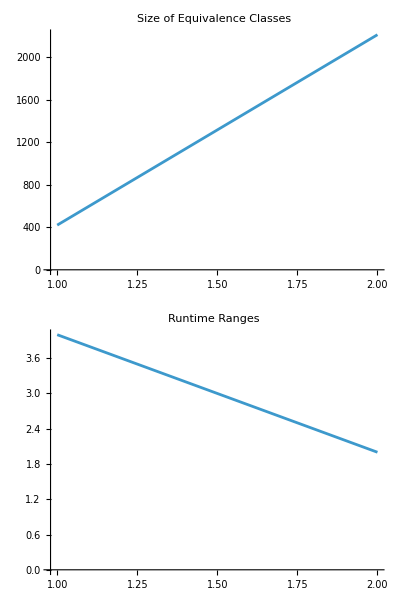

```mathematica
Column[
With[
{w=1600},
{
ListPlot[
Length/@eqlgroups[[11;;12]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes"
],
ListPlot[
haltdifs[[All,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}
]
]
```